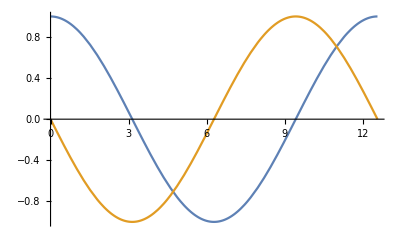

```mathematica
wMatrixRWA=Ω/2 PauliMatrix[2];
stateVec=Table[Subscript[c, i][t],{i,2}];
initStateVec={1,0};
tdseEqnsRWA=Table[{Subscript[c, i]'[t]==I(wMatrixRWA.stateVec)[[i]],Subscript[c, i][0]==initStateVec[[i]]},{i,2}];
tMax=4 Pi;
solRWA=NDSolve[tdseEqnsRWA/.Ω->1,stateVec,{t,0,tMax}];
solFnRWA=stateVec/.First[solRWA];
Plot[solFnRWA,{t,0,tMax}]
```

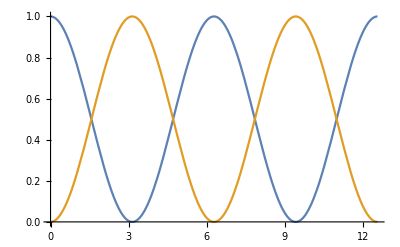

```mathematica
solFnRWAProb=Abs[solFnRWA]^2;
Plot[solFnRWAProb,{t,0,tMax}]
```

i) The plot shows the probabilities for the upper (blue line) and lower (red line) eigenstate as functions of time after setting up the system as in the upper energy state and letting it evolve with time.